```mathematica
Lx=20
Ly=20
```

20

20

```mathematica
(*--------------------Projected Brane--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

800

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
(** Comment/Uncomment the rational and irrational equations accordingly **)
```

```mathematica
(**-------Irrational-------**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+22
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+12
```

```mathematica
(**-------Rational-------**)
```

```mathematica
(** LineUp[x_]:=(2/3)(x-1)+22
LineDn[x_]:=(2/3)*(x-2)+12 **)
```

```mathematica
GreenSites=Table[{i,Ly/2},{i,1,Lx}];
```

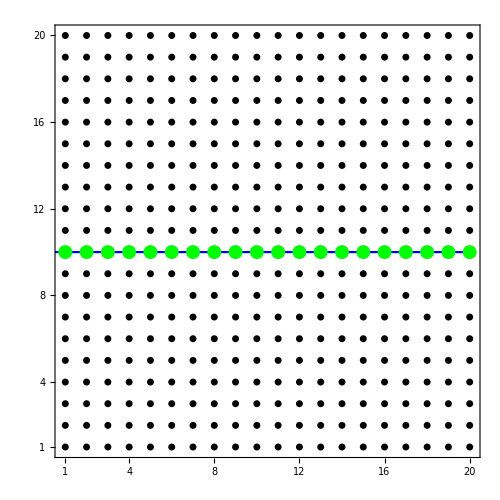

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
Plot[Ly/2,{x,0,Lx},PlotStyle-> Blue],
ListPlot[GreenSites,PlotStyle-> {Green,PointSize[0.02]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle->24,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```